```mathematica
<<Util`
```

```mathematica
<<PSD`
```

```mathematica
ReadEventDat[datpath<>"/eventTS.csv"]
```

```mathematica
dat=Import["/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/temp.txt","CSV"];//AbsoluteTiming
```

{0.27058,Null}

```mathematica
Length[dat]
```

73

```mathematica
Manipulate[ListLinePlot[Abs[dat⟦i⟧],PlotRange->All],{i,1,Length[dat],1}]
```

```mathematica
bdepth=Import["/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/temp.txt","CSV"];//AbsoluteTiming
```

{0.01546,Null}

```mathematica
bdepthhi=Import["/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/temp.txt","CSV"];//AbsoluteTiming
```

{0.01852,Null}

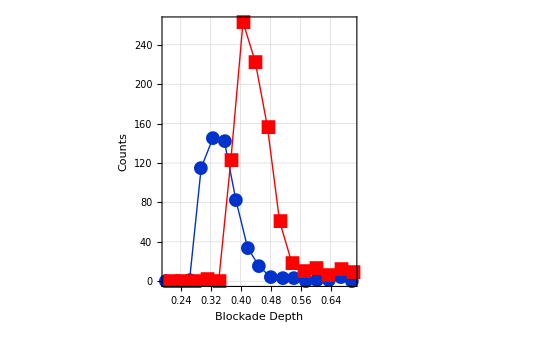

```mathematica
ListLinePlot[{
Hist1D[Flatten[bdepth],{0,1},0.031],
Hist1D[Flatten[bdepthhi],{0,1},0.0325]
},PlotMarkers->{Automatic,18},Joined->True,GridLines->Automatic,GridLinesStyle->Dashed,PlotRange->{{0.2,0.7},All},Frame->True,FrameLabel->{Style["Blockade Depth",20,FontFamily->"Helvetica"],Style["Counts",20,FontFamily->"Helvetica"]},PlotStyle->{{Thick,RGBColor[0,50/255,204/255]},{Thick,Red}},FrameTicksStyle->Directive[20,FontFamily->"Helvetica"]]
```

```mathematica
evnt=Import["/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/temp.txt","CSV"];//AbsoluteTiming
```

{0.01669,Null}

```mathematica
ReadEventDat[fname_]:=Import[fname,"CSV"]
ReadEventMeta[fname_]:=Import[fname,"TSV"]⟦2;;⟧
ReadEventMetaColNames[fname_]:=Block[{tab},(tab[#⟦1⟧]=#⟦2⟧)&/@Transpose[{Import[fname,"TSV"]⟦1⟧,Range[Length[Import[datpath<>"/eventMD.tsv","TSV"]⟦1⟧]]}];
Return[tab]
]
DisplayEvents[eventMD_,eventTS_]:=
Manipulate[ListLinePlot[eventTS⟦i⟧,PlotRange->All,Epilog->{Black,Thick,Line[{{0,eventMD⟦i⟧⟦3⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦3⟧}}],Line[{{0,eventMD⟦i⟧⟦2⟧},{Length[eventTS⟦i⟧],eventMD⟦i⟧⟦2⟧}}],Red,Line[{{eventMD⟦i⟧⟦4⟧,-400},{eventMD⟦i⟧⟦4⟧,400}}],Line[{{eventMD⟦i⟧⟦5⟧,-400},{eventMD⟦i⟧⟦5⟧,400}}]}],{i,1,Length[eventTS],1}]
```

```mathematica
datpath="/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV";
```

```mathematica
DisplayEvents[ReadEventMeta[datpath<>"/eventMD.tsv"],ReadEventDat[datpath<>"/eventTS.csv"]]
```

```mathematica
Gauss1D[x_,α_,μ_,σ_]:=α Exp[-(x-μ)^2/(2 σ^2)]
```

```mathematica
ToString[NonlinearModelFit[PDF1D[Abs[ReadEventDat[datpath<>"/eventTS.csv"]⟦14⟧],{0,150},0.5],
Gauss1D[x,α1,μ1,σ1]+Gauss1D[x,α2,μ2,σ2],
{{α1,0.02},{μ1,30},{σ1,10},{α2,0.04},{μ2,110},{σ2,5}},x]["BestFitParameters"]]
```

{α1 -> 0.00649496, μ1 -> 108.243, σ1 -> 10.6935, α2 -> 0.0551257, μ2 -> 113.577, σ2 -> 5.92514}

```mathematica
Manipulate[Block[{ft},
ft=NonlinearModelFit[PDF1D[Abs[ReadEventDat[datpath<>"/eventTS.csv"]⟦i⟧],{0,150},1],
Gauss1D[x,α1,μ1,σ1]+Gauss1D[x,α2,μ2,σ2],
{{α1,0.02},{μ1,30},{σ1,10},{α2,0.04},{μ2,110},{σ2,5}},x];
GraphicsRow[{
ListLinePlot[ReadEventDat[datpath<>"/eventTS.csv"]⟦i⟧,PlotRange->All],
Show[{
ListPlot[PDF1D[Abs[ReadEventDat[datpath<>"/eventTS.csv"]⟦i⟧],{0,150},1],PlotRange->All,PlotMarkers->Automatic, Epilog->Text[ToString[ft["BestFitParameters"]],{50,0.03}]],
Plot[Evaluate[Normal[ft]],{x,0,150},PlotStyle->{Thick,Black}
]
}]
}]
],{i,1,198,1}]
```

```mathematica
?Gauss1D
```

Global`Gauss1D

Gauss1D[x_,α_,μ_,σ_]:=α Exp[-(x-μ)^2/(2 σ^2)]

```mathematica
ReadPyEventMeta[fname_]:=Block[{dat=Import[fname]⟦2;;⟧},
Return[Table[ToExpression[StringSplit[ToString[#],{"+/-"}]&/@dat⟦i⟧],{i,Length[dat]}]]
]
```

```mathematica
prange[dat_]:={All,0}/;Mean[dat]<0
prange[dat_]:={0,All}
```

```mathematica
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts⟦md⟦4⟧⟦1⟧-50;;md⟦5⟧⟦1⟧+50⟧,PlotRange->prange[ts],Frame->True,Epilog->{
Black,Thickness[Small],
 Line[{{0,md⟦2⟧⟦1⟧},{10000,md⟦2⟧⟦1⟧}}], Line[{{0,md⟦3⟧⟦1⟧},{10000,md⟦3⟧⟦1⟧}}], 
Red,Thickness[Small],
 Line[{{50-1,-500},{50-1,500}}],Line[{{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,-500},{50+(md⟦5⟧⟦1⟧-md⟦4⟧⟦1⟧)+1,500}}],
Blue,Text[Style[md⟦1⟧⟦1⟧,20],{50,txtpos}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evntplot[ts_,md_, txtpos_]:=ListLinePlot[ts,PlotRange->prange[ts],Frame->True,PlotStyle->Gray,Epilog->{Red,Text[Style[md⟦1⟧⟦1⟧,20],{Length[ts]/2,txtpos}]}]
```

```mathematica
evnthist[ts_,md_]:=Show[{
ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,Frame->True,Epilog->{Black,Text[Style["o="<>ToString[md⟦2⟧⟦1⟧]<>"±"<>ToString[md⟦2⟧⟦2⟧]<>"\nb="<>ToString[md⟦3⟧⟦1⟧]<>"±"<>ToString[md⟦3⟧⟦2⟧],16],{70,0.02}]}],
Plot[Gauss1D[x,md⟦8⟧⟦2⟧,Abs[md⟦2⟧⟦1⟧],md⟦2⟧⟦2⟧]+Gauss1D[x,md⟦8⟧⟦1⟧,Abs[md⟦3⟧⟦1⟧],md⟦3⟧⟦2⟧],{x,0,150},PlotStyle->{Black,Thick}]
}]/;ToString[md⟦1⟧⟦1⟧]=="normal"
evnthist[ts_,md_]:=ListPlot[PDF1D[Abs[ts],{0,Max[Abs[ts]]+20},1],PlotRange->All,PlotMarkers->Automatic,PlotStyle->Gray,Frame->True]
```

```mathematica
pydispevent[ts_,md_,txtpos_:-30]:=Manipulate[
GraphicsRow[{
evntplot[ts⟦i⟧,md⟦i⟧,txtpos],
evnthist[ts⟦i⟧,md⟦i⟧]
}],{i,1,Length[ts],1}
]
```

```mathematica
"/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/tf.tsv"
```

/Users/balijepalliak/Research/Experiments/AnalysisTools/pyEventAnalysis/tf.tsv

```mathematica
datpath="/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/"
```

/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/

```mathematica
pydispevent[ReadEventDat[datpath<>"/eventTS.csv"],ReadPyEventMeta[datpath<>"/eventMD.tsv"],-20]
```

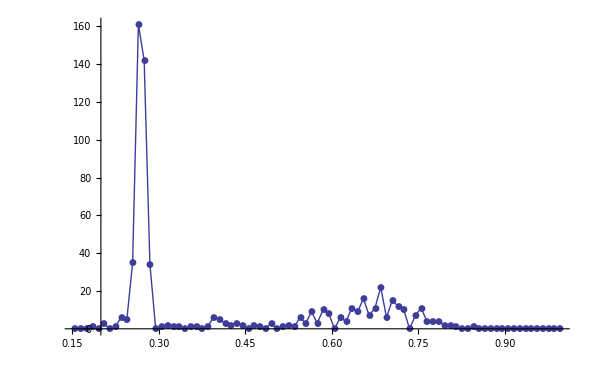

```mathematica
ListLinePlot[Hist1D[Select[ReadPyEventMeta[datpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,1},0.01],PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
aa=Evaluate[Normal[NonlinearModelFit[Hist1D[Select[ReadPyEventMeta[datpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,1},0.01],a Exp[-b t],{{a,100},{b,2}},t]]]
```

27.3746 ⅇ^(-2.54695 t)

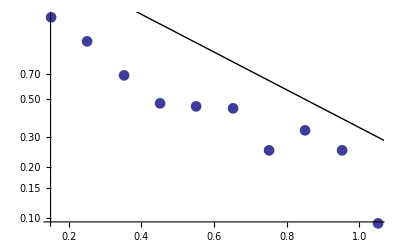

```mathematica
Show[{
ListLogPlot[PDF1D[Select[Flatten[ReadPyEventMeta[datpath<>"/eventMD.tsv"]⟦All,7⟧],#≠-1&],{0.1,1.1},0.1],PlotRange->All,Joined->False,PlotMarkers->{Automatic,14}],
LogPlot[Evaluate[Normal[NonlinearModelFit[PDF1D[Select[ReadPyEventMeta[datpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,1},0.01],a Exp[-b t],{{a,.5},{b,2}},t]]],{t,0,1.2},PlotStyle->{Black,Thick}]
}]
```

```mathematica
goldpath="/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS"
```

/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/Take2LongerDataPNAS

```mathematica
pydispevent[ReadEventDat[goldpath<>"/eventTS.csv"],ReadPyEventMeta[goldpath<>"/eventMD.tsv"],{100,30}]
```

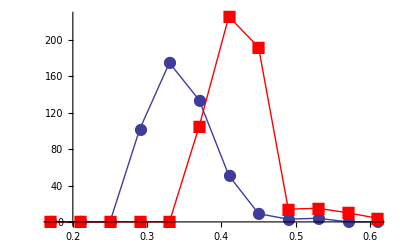

```mathematica
ListLinePlot[{
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD_low.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04],
Hist1D[Select[ReadPyEventMeta[goldpath<>"/eventMD.tsv"]⟦All,6⟧⟦All,1⟧,#≠-1&],{0.15,0.65},0.04]
},PlotRange->All,PlotMarkers->{Automatic,16},PlotStyle->{Thick,{Red,Thick}}]
```

```mathematica
Block[{ts=ReadEventDat["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventTS.csv"], md=ReadEventMeta["/Users/balijepalliak/Research/Experiments/PEG29EBSRefData/GoldHeating/SteadyStateHeating/20120725/21Cr1M40mV/eventMD.tsv"]},
Manipulate[DisplayEvent[ts⟦i⟧,md⟦i⟧],{i,1,Length[ts],1}]
]
```

```mathematica
evnt⟦48⟧⟦;;5⟧
```

{-84.9027,-113.895,501,512,-102.786}

```mathematica
Manipulate[DisplayEvent[evnt⟦i⟧],{i,1,Length[evnt],1}]
```

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}
```

{113.143,113.841}

```mathematica
{MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]//Mean,MovingAverage[Abs[evnt⟦8⟧⟦evnt⟦8⟧⟦4⟧+55;;⟧],100]//Mean}//Mean
```

113.492

```mathematica
DSolve[t''[x]+q/κ==0,t,x]
```

{{t→Function[{x},-(q x^2)/(2 κ)+C[1]+x C[2]]}}

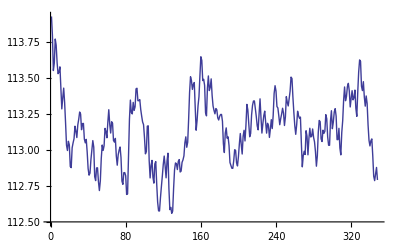

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;evnt⟦8⟧⟦3⟧-50⟧],100]]
```

```mathematica
evnt⟦8⟧⟦4⟧
```

1091

```mathematica
evnt⟦8⟧⟦5;;⟧
```

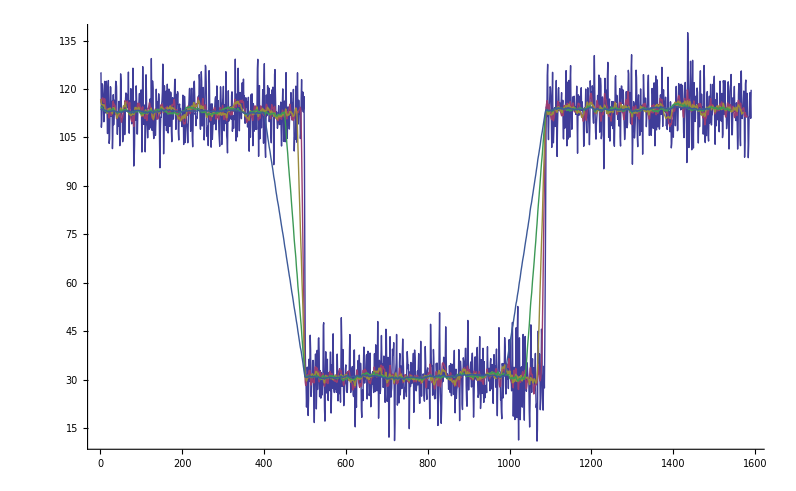

```mathematica
ListLinePlot[MovingAverage[Abs[evnt⟦8⟧⟦5;;⟧],#]&/@{1,10,20,50,100},PlotRange->All]
```

```mathematica
DSolve[{D[f[t], t]==k c (1-f[t]/fmax)- kd f[t]},f[t],t]
```

{{f[t]→(c ⅇ^(((-c k-fmax kd) t)/fmax+((c k+fmax kd) t)/fmax) fmax k)/(c k+fmax kd)+ⅇ^(((-c k-fmax kd) t)/fmax) C[1]}}